```mathematica
col[{m_,n_}]:=irisAll⟦All,{m,n}⟧;
names=Subsets[Range@4,{2}]
```

{{1,2},{1,3},{1,4},{2,3},{2,4},{3,4}}

```mathematica
toSubscript[{m_,n_}]:=ToExpression @ SubscriptBox[x,#]&/@{m,n}
```

```mathematica
vars=toSubscript/@names
```

{{x_1,x_2},{x_1,x_3},{x_1,x_4},{x_2,x_3},{x_2,x_4},{x_3,x_4}}

```mathematica
classes=col/@names;
```

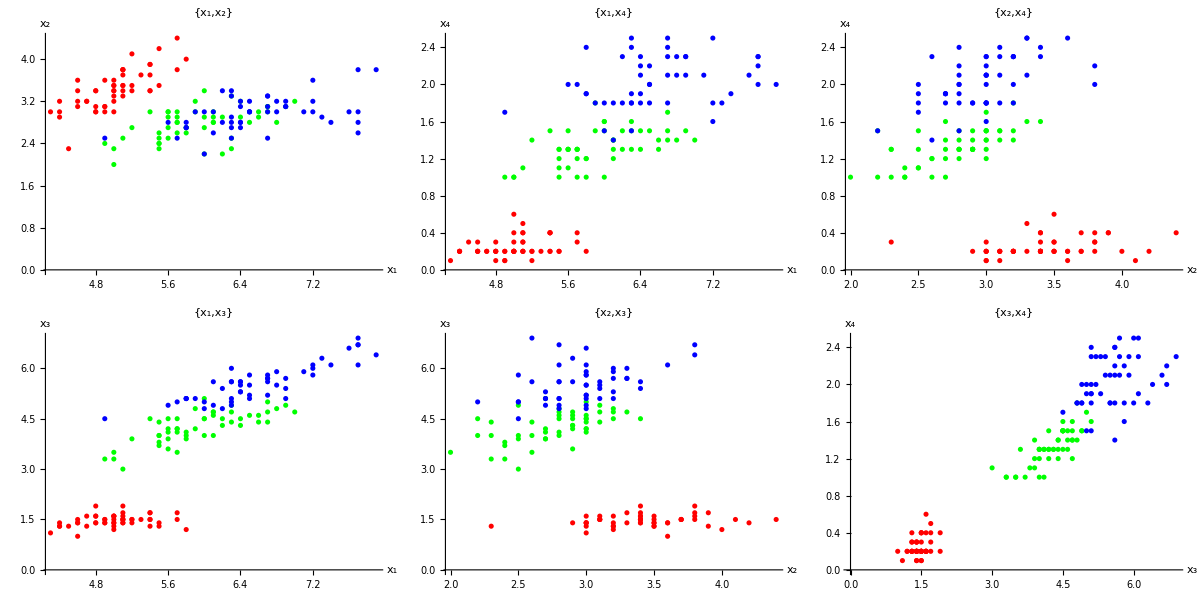

```mathematica
Multicolumn[ListPlot[Partition[classes⟦#⟧,50],AxesLabel->vars⟦#⟧,PlotLabel->vars⟦#⟧,PlotStyle->{Red,Green,Blue}]&/@Range[6],3]
```